```mathematica
Solve[D[Log[w*L+π]+Log[1-L],L]==0]
```

{{L→(-π+w)/(2 w)}}

```mathematica
D[Log[Co]+ψ*Log[l]+λ*(w*h+pi-T-Co-w*l),Co]
```

1/Co-λ

```mathematica
D[Log[Co]+ψ*Log[l]+λ*(w*h+pi-T-Co-w*l),l]
```

-w λ+ψ/l

```mathematica
Solve[{1/Co-λ==0,-w λ+ψ/l==0,w*h+pi-T-Co-w*l==0},{Co,l,λ}]
```

{{Co→(pi-T+h w)/(1+ψ),l→(pi ψ-T ψ+h w ψ)/(w (1+ψ)),λ→(1+ψ)/(pi-T+h w)}}

```mathematica
2.75+2.5*4+4.5+4.75+4+4.75+4.75
```

35.5

```mathematica
Solve[D[Log[x]-x-x^2,x]==0,x]
```

{{x→-1},{x→1/2}}

```mathematica
Solve[D[Sqrt[(1-τ)*n]-n,n]==0]
```

{{τ→1-4 n}}

```mathematica
Solve[D[Sqrt[(1-τ)*n]-n,n]==0,n]
```

{{n→(1-τ)/4}}

```mathematica
(1-τ)*(1-τ)/4
```

1/4 (1-τ)^2

```mathematica
D[Sqrt[n],n]
```

1/(2 √n)

```mathematica
Sqrt[(1-τ)*n]
```

√(n (1-τ))

```mathematica
{(1-τ)*(1-τ)/4,(1-τ)/4,(Log[(1-τ)*(1-τ)/4]-(1-τ)/4)}/.{τ->0}//N
{(1-τ)*(1-τ)/4,(1-τ)/4,(Log[(1-τ)*(1-τ)/4]-(1-τ)/4)}/.{τ->0.5}//N
```

{0.25,0.25,-1.63629}

{0.0625,0.125,-2.89759}

```mathematica
-D[Sqrt[c]+(1-n),n]/D[Sqrt[c]+(1-n),c]
```

```mathematica
2 √c/.{c->0.0625}
```

0.5

```mathematica
Solve[D[Sqrt[n*w+π-T]+Sqrt[1-n],n]==0,n]
```

{{n→(-π+T+w^2)/(w (1+w))}}

```mathematica
Dt[τ*L[τ]]/.{L'[τ]->0}
```

Dt[τ] L[τ]

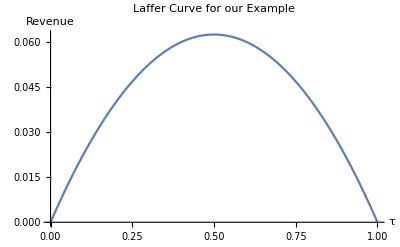

```mathematica
temp=Plot[τ*(1-τ)/4,{τ,0,1},PlotLabel->"Laffer Curve for our Example",AxesLabel->{"τ","Revenue"}]
```

```mathematica
Export["~/Dropbox/Econ 352/Summer 2022/Figures/Laffer.png",temp]
```

~/Dropbox/Econ 352/Summer 2022/Figures/Laffer.png

```mathematica
(1-τ)/4/.(Solve[τ*(1-τ)/4==0.03])
```

{0.215139,0.0348612}

```mathematica
(1-τ)^2/4/.(Solve[τ*(1-τ)/4==0.03])
```

{0.185139,0.00486122}

```mathematica
(Sqrt[(1-τ)^2/4]-(1-τ)/4)/.{(Solve[τ*(1-τ)/4==0.03])}
```

{{0.215139,0.0348612}}

```mathematica
Solve[((Sqrt[(1-τ)^2/4-z]-(1-τ)/4)/.{τ->0.21513878188659974})==0.0348612]
```

{{z→0.100605}}